```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_LTC/";*)
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BTC Price | log return future | log return bitcoin
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 40143.7 | 0.0212907 | 0.018658
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 39401.7 | -0.0904653 | -0.0934764
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 43262.4 | -0.0196938 | -0.0216123
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 44207.6 | -0.131645 | -0.126287
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 50158.3 | 0.03685 | 0.0328265
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 48538.5 | -0.119603 | -0.11567
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 54490.5 | -0.042369 | -0.0388241
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 56647.7 | 0.018947 | 0.0163419
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 55729.5 | -0.0359909 | -0.0331504)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return bitcoin

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=104, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

104

103

102

101

100

99

98

97

96

95

94

93

92

91

90

89

88

87

86

85

84

83

82

81

80

79

78

77

76

75

74

73

72

71

70

69

68

67

66

65

64

63

62

61

60

59

58

57

56

55

54

53

52

51

50

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{0.898266,0.0439898}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_Tiingo/

```mathematica
For[kk=0, kk≤111, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.993083617458712}. NIntegrate obtained 0.134005 and 0.000123554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.993083617458712}. NIntegrate obtained 0.1403 and 0.000133509 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.993083617458712}. NIntegrate obtained 0.0751751 and 0.000112086 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

81

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

82

Risk Measures...

Variance

VaR 99

VaR 95

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ES 99

ES 95

Spectral 10

83

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

84

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

85

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

86

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

87

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

88

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

89

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

90

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

107

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

108

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

109

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

110

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

111

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.99034 | 0.918635 | 0.944885 | 0.852601 | 0.910033 | 0.934942
 | 2021-05-13 | 0.990767 | 0.92801 | 0.95229 | 0.887328 | 0.924358 | 0.933327
 | 2021-05-06 | 0.990485 | 0.927728 | 0.951782 | 0.886263 | 0.921027 | 0.93314
 | 2021-04-29 | 0.989831 | 0.927431 | 0.950223 | 0.88387 | 0.918781 | 0.93138
 | 2021-04-22 | 0.989901 | 0.927431 | 0.948724 | 0.884382 | 0.918663 | 0.930175
 | 2021-04-15 | 0.989258 | 0.927431 | 0.948876 | 0.880233 | 0.915778 | 0.929706
 | 2021-04-08 | 0.989365 | 0.927431 | 0.948219 | 0.880167 | 0.915593 | 0.930927
 | 2021-04-01 | 0.989693 | 0.927431 | 0.948469 | 0.882854 | 0.917104 | 0.93306
 | 2021-03-25 | 0.98998 | 0.927431 | 0.949328 | 0.884973 | 0.91824 | 0.933294
 | 2021-03-18 | 0.989966 | 0.927431 | 0.949496 | 0.884969 | 0.918292 | 0.934081
 | 2021-03-11 | 0.990055 | 0.927431 | 0.948975 | 0.884276 | 0.917986 | 0.93495
 | 2021-03-04 | 0.989241 | 0.927431 | 0.946741 | 0.878494 | 0.914439 | 0.931877
 | 2021-02-25 | 0.988807 | 0.927431 | 0.949186 | 0.876458 | 0.914747 | 0.931421
 | 2021-02-18 | 0.989342 | 0.927431 | 0.948787 | 0.880468 | 0.913838 | 0.934858
 | 2021-02-10 | 0.989315 | 0.927431 | 0.948325 | 0.881377 | 0.913935 | 0.934764
 | 2021-02-03 | 0.989064 | 0.927431 | 0.948517 | 0.883455 | 0.914843 | 0.931971
 | 2021-01-27 | 0.988705 | 0.927431 | 0.948335 | 0.879545 | 0.912797 | 0.929823
 | 2021-01-20 | 0.988985 | 0.927648 | 0.949186 | 0.882864 | 0.913129 | 0.93229
 | 2021-01-12 | 0.987865 | 0.927431 | 0.944299 | 0.879175 | 0.907836 | 0.929862
 | 2021-01-05 | 0.987531 | 0.916295 | 0.944608 | 0.875317 | 0.90024 | 0.930132
 | 2020-12-28 | 0.987606 | 0.930121 | 0.946331 | 0.873975 | 0.904215 | 0.929042
 | 2020-12-18 | 0.988505 | 0.923444 | 0.948249 | 0.881535 | 0.907284 | 0.932566
 | 2020-12-11 | 0.987107 | 0.923444 | 0.948178 | 0.87779 | 0.905033 | 0.930549
 | 2020-12-04 | 0.987119 | 0.923444 | 0.949046 | 0.878007 | 0.905245 | 0.930279
 | 2020-11-27 | 0.987881 | 0.941209 | 0.951063 | 0.882022 | 0.916995 | 0.925618
 | 2020-11-19 | 0.986831 | 0.941223 | 0.950234 | 0.878068 | 0.912728 | 0.926884
 | 2020-11-12 | 0.988418 | 0.950387 | 0.957286 | 0.88715 | 0.921017 | 0.935226
 | 2020-11-05 | 0.986798 | 0.938313 | 0.947075 | 0.876611 | 0.910699 | 0.928077
 | 2020-10-29 | 0.988444 | 0.950387 | 0.952458 | 0.887925 | 0.920667 | 0.93665
 | 2020-10-22 | 0.986648 | 0.938196 | 0.946932 | 0.876559 | 0.910487 | 0.926204
 | 2020-10-15 | 0.984777 | 0.936868 | 0.945551 | 0.86961 | 0.908401 | 0.922694
 | 2020-10-08 | 0.985391 | 0.936362 | 0.945299 | 0.86782 | 0.907328 | 0.924238
 | 2020-10-01 | 0.982893 | 0.926702 | 0.940104 | 0.855491 | 0.898097 | 0.914766
 | 2020-09-24 | 0.983833 | 0.930769 | 0.942243 | 0.860273 | 0.902026 | 0.917358
 | 2020-09-17 | 0.983921 | 0.928824 | 0.942525 | 0.857123 | 0.904284 | 0.917338
 | 2020-09-10 | 0.984238 | 0.930476 | 0.942252 | 0.857061 | 0.904121 | 0.917759
 | 2020-09-02 | 0.98435 | 0.937778 | 0.939497 | 0.872865 | 0.909484 | 0.916666
 | 2020-08-26 | 0.984194 | 0.937097 | 0.937887 | 0.869547 | 0.907529 | 0.91678
 | 2020-08-19 | 0.985965 | 0.947206 | 0.949058 | 0.878996 | 0.916822 | 0.927
 | 2020-08-12 | 0.985951 | 0.947202 | 0.948194 | 0.878942 | 0.916613 | 0.927171
 | 2020-08-05 | 0.982481 | 0.912753 | 0.917807 | 0.857188 | 0.892306 | 0.899596
 | 2020-07-29 | 0.984824 | 0.936702 | 0.941824 | 0.868544 | 0.910294 | 0.919456
 | 2020-07-22 | 0.985346 | 0.936639 | 0.941574 | 0.872185 | 0.913169 | 0.918219
 | 2020-07-15 | 0.983726 | 0.929923 | 0.938608 | 0.859557 | 0.905942 | 0.917442
 | 2020-07-08 | 0.983955 | 0.931067 | 0.940024 | 0.860084 | 0.907002 | 0.917855
 | 2020-06-30 | 0.973976 | 0.907795 | 0.92858 | 0.818569 | 0.882238 | 0.894173
 | 2020-06-23 | 0.974229 | 0.907227 | 0.92858 | 0.819705 | 0.882613 | 0.894743
 | 2020-06-16 | 0.974994 | 0.907396 | 0.92858 | 0.821238 | 0.883585 | 0.896071
 | 2020-06-09 | 0.97473 | 0.895336 | 0.918733 | 0.813857 | 0.872885 | 0.890201
 | 2020-06-02 | 0.974299 | 0.897426 | 0.918299 | 0.812356 | 0.872441 | 0.889232
 | 2020-05-26 | 0.973717 | 0.894209 | 0.916542 | 0.810316 | 0.870538 | 0.887566
 | 2020-05-18 | 0.973031 | 0.892174 | 0.915105 | 0.80775 | 0.868678 | 0.885731
 | 2020-05-11 | 0.971477 | 0.888718 | 0.909795 | 0.803916 | 0.864848 | 0.883137
 | 2020-05-04 | 0.970584 | 0.872321 | 0.876651 | 0.811626 | 0.846403 | 0.860662
 | 2020-04-27 | 0.971101 | 0.87387 | 0.877869 | 0.813603 | 0.848697 | 0.859102
 | 2020-04-20 | 0.968328 | 0.868662 | 0.872698 | 0.805269 | 0.840695 | 0.850567
 | 2020-04-13 | 0.966381 | 0.864932 | 0.872026 | 0.798432 | 0.836298 | 0.855666
 | 2020-04-03 | 0.965962 | 0.863283 | 0.866085 | 0.797687 | 0.833934 | 0.84858
 | 2020-03-27 | 0.964657 | 0.876685 | 0.895163 | 0.789037 | 0.84727 | 0.864486
 | 2020-03-20 | 0.968298 | 0.900462 | 0.919726 | 0.802647 | 0.868451 | 0.883269
 | 2020-03-13 | 0.957953 | 0.864712 | 0.883004 | 0.77448 | 0.834254 | 0.844269
 | 2020-03-06 | 0.956729 | 0.820924 | 0.841648 | 0.756264 | 0.791622 | 0.83129
 | 2020-02-28 | 0.956259 | 0.813736 | 0.803973 | 0.767629 | 0.782681 | 0.817113
 | 2020-02-21 | 0.954625 | 0.806124 | 0.811806 | 0.760631 | 0.776846 | 0.818629
 | 2020-02-13 | 0.956129 | 0.80803 | 0.822746 | 0.758325 | 0.783398 | 0.824222
 | 2020-02-06 | 0.957094 | 0.806055 | 0.813434 | 0.76097 | 0.780582 | 0.825364
 | 2020-01-30 | 0.955366 | 0.801416 | 0.823147 | 0.742538 | 0.79046 | 0.821151
 | 2020-01-23 | 0.955131 | 0.822772 | 0.86148 | 0.73831 | 0.807503 | 0.822581
 | 2020-01-15 | 0.951708 | 0.833792 | 0.893054 | 0.70638 | 0.814278 | 0.840346
 | 2020-01-08 | 0.9495 | 0.823621 | 0.871484 | 0.715413 | 0.803812 | 0.824774
 | 2019-12-31 | 0.947555 | 0.818963 | 0.866778 | 0.712045 | 0.801028 | 0.819506
 | 2019-12-23 | 0.93572 | 0.791068 | 0.84942 | 0.677111 | 0.773427 | 0.795804
 | 2019-12-16 | 0.934785 | 0.795556 | 0.852722 | 0.675492 | 0.774741 | 0.792808
 | 2019-12-09 | 0.934978 | 0.796724 | 0.854457 | 0.676331 | 0.776193 | 0.794073
 | 2019-12-02 | 0.93378 | 0.787286 | 0.834148 | 0.685376 | 0.769249 | 0.77989
 | 2019-11-22 | 0.934162 | 0.796295 | 0.853471 | 0.676745 | 0.775884 | 0.791521
 | 2019-11-15 | 0.931317 | 0.789872 | 0.84625 | 0.675046 | 0.771729 | 0.783648
 | 2019-11-08 | 0.934929 | 0.796237 | 0.853564 | 0.676436 | 0.775953 | 0.792567
 | 2019-11-01 | 0.934226 | 0.785957 | 0.835202 | 0.685765 | 0.769946 | 0.780558
 | 2019-10-25 | 0.934546 | 0.798324 | 0.857374 | 0.676299 | 0.778254 | 0.794284
 | 2019-10-18 | 0.934235 | 0.799792 | 0.849912 | 0.681882 | 0.778783 | 0.788947
 | 2019-10-11 | 0.935148 | 0.793244 | 0.853032 | 0.680618 | 0.778597 | 0.786569
 | 2019-10-04 | 0.935934 | 0.809433 | 0.883761 | 0.670808 | 0.79261 | 0.806406
 | 2019-09-27 | 0.936707 | 0.802169 | 0.864377 | 0.682035 | 0.784992 | 0.795379
 | 2019-09-20 | 0.937616 | 0.796697 | 0.846188 | 0.688481 | 0.773935 | 0.795793
 | 2019-09-13 | 0.93771 | 0.798879 | 0.851096 | 0.689161 | 0.776125 | 0.799428
 | 2019-09-06 | 0.938816 | 0.798822 | 0.845001 | 0.690161 | 0.773001 | 0.799436
 | 2019-08-29 | 0.936449 | 0.803652 | 0.877524 | 0.672832 | 0.779331 | 0.807038
 | 2019-08-22 | 0.937248 | 0.79892 | 0.857492 | 0.684359 | 0.774894 | 0.798475
 | 2019-08-15 | 0.936484 | 0.803312 | 0.884847 | 0.668272 | 0.782527 | 0.806075
 | 2019-08-08 | 0.936891 | 0.800986 | 0.874137 | 0.679635 | 0.78247 | 0.801125
 | 2019-08-01 | 0.937275 | 0.8019 | 0.875012 | 0.683945 | 0.785355 | 0.799582
 | 2019-07-25 | 0.939314 | 0.80705 | 0.873799 | 0.687556 | 0.786157 | 0.800807
 | 2019-07-18 | 0.940273 | 0.806516 | 0.876683 | 0.689027 | 0.788608 | 0.803859
 | 2019-07-11 | 0.939637 | 0.804455 | 0.85901 | 0.694309 | 0.782943 | 0.799497
 | 2019-07-03 | 0.939919 | 0.81168 | 0.864679 | 0.69771 | 0.786743 | 0.802916
 | 2019-06-26 | 0.937757 | 0.762031 | 0.843605 | 0.610425 | 0.757964 | 0.803961
 | 2019-06-19 | 0.933914 | 0.739609 | 0.80553 | 0.635972 | 0.743649 | 0.773086
 | 2019-06-12 | 0.935549 | 0.762243 | 0.84029 | 0.622484 | 0.759922 | 0.786359
 | 2019-06-05 | 0.937314 | 0.761177 | 0.86627 | 0.613358 | 0.763768 | 0.792834
 | 2019-05-29 | 0.936063 | 0.759998 | 0.8651 | 0.613988 | 0.758175 | 0.79115
 | 2019-05-21 | 0.933495 | 0.742762 | 0.836064 | 0.629809 | 0.746518 | 0.767925
 | 2019-05-14 | 0.935475 | 0.753685 | 0.852214 | 0.627311 | 0.75677 | 0.778286
 | 2019-05-07 | 0.938191 | 0.768017 | 0.878568 | 0.623685 | 0.770864 | 0.780648
 | 2019-04-30 | 0.939397 | 0.766659 | 0.882835 | 0.62272 | 0.776121 | 0.778095
 | 2019-04-23 | 0.948508 | 0.781436 | 0.884035 | 0.648501 | 0.787441 | 0.801187
 | 2019-04-15 | 0.950087 | 0.777365 | 0.879781 | 0.658205 | 0.787257 | 0.800777
 | 2019-04-08 | 0.951043 | 0.783098 | 0.892836 | 0.665994 | 0.799413 | 0.810041
 | 2019-04-01 | 0.947418 | 0.758266 | 0.8573 | 0.68888 | 0.78099 | 0.773577
 | 2019-03-25 | 0.948262 | 0.82421 | 0.890725 | 0.707887 | 0.803974 | 0.794702
 | 2019-03-18 | 0.948909 | 0.818899 | 0.874502 | 0.719133 | 0.799751 | 0.780167
 | 2019-03-11 | 0.950391 | 0.812073 | 0.86771 | 0.726487 | 0.797823 | 0.782279

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.998676 | 0.963165 | 0.987869 | 0.966717 | 0.979752 | 0.958353
 | 2021-05-13 | 0.998496 | 0.932669 | 0.946055 | 0.933074 | 0.941005 | 1.02332
 | 2021-05-06 | 0.999115 | 0.971516 | 0.98436 | 0.971816 | 0.983237 | 0.932887
 | 2021-04-29 | 0.999015 | 0.97392 | 0.946629 | 0.97392 | 0.956319 | 0.965065
 | 2021-04-22 | 0.998375 | 0.950825 | 0.964773 | 0.950825 | 0.960714 | 0.962503
 | 2021-04-15 | 0.990547 | 0.934551 | 0.952178 | 0.934551 | 0.945059 | 0.556582
 | 2021-04-08 | 0.989946 | 0.957609 | 0.928395 | 0.957609 | 0.940345 | 0.896937
 | 2021-04-01 | 0.969785 | 0.931733 | 0.916069 | 0.931733 | 0.922317 | 0.743296
 | 2021-03-25 | 0.972114 | -0.0897622 | -0.17744 | -0.0897622 | -0.141549 | 0.968066
 | 2021-03-18 | 0.995049 | 0.959149 | 0.974454 | 0.959149 | 0.967925 | 0.827293
 | 2021-03-11 | 0.995338 | 0.938476 | 0.95393 | 0.938476 | 0.94767 | 0.913161
 | 2021-03-04 | 0.970488 | 1.1389 | 1.16012 | 1.1389 | 1.15171 | 0.953612
 | 2021-02-25 | 0.987968 | 0.807197 | 0.822598 | 0.807197 | 0.816497 | 0.939442
 | 2021-02-18 | 0.995107 | 0.964224 | 0.959143 | 0.964224 | 0.961174 | 0.860628
 | 2021-02-10 | 0.98678 | 0.0946105 | -0.442268 | 0.0946103 | -0.229611 | 0.906634
 | 2021-02-03 | 0.999642 | 0.995577 | 0.99433 | 0.995577 | 0.994832 | 0.98156
 | 2021-01-27 | 0.984278 | 0.682749 | 0.626453 | 0.682749 | 0.648813 | 0.951199
 | 2021-01-20 | 0.992832 | 0.950754 | 0.975788 | 0.95752 | 0.968285 | 0.824349
 | 2021-01-12 | 0.998715 | 0.986537 | 0.981516 | 0.986537 | 0.983739 | 0.945973
 | 2021-01-05 | 0.994112 | 0.937399 | 0.924038 | 0.937399 | 0.939509 | 0.911133
 | 2020-12-28 | 0.977236 | 3.15532 | 3.01984 | 2.95111 | 3.28793 | 0.948096
 | 2020-12-18 | 0.997585 | 1.16739 | 1.41732 | 1.16739 | 1.60469 | 0.946528
 | 2020-12-11 | 0.992993 | -0.050918 | -0.19061 | -0.0440023 | -0.861807 | 0.945791
 | 2020-12-04 | 0.970517 | 0.832504 | 0.838862 | 0.832504 | 0.848588 | 0.450642
 | 2020-11-27 | 0.987717 | 0.303545 | 0.238562 | 0.389819 | 0.289412 | 0.972517
 | 2020-11-19 | 0.996634 | 0.983369 | 0.979538 | 0.988428 | 0.982361 | 0.806417
 | 2020-11-12 | 0.994604 | 0.229343 | 0.478897 | 0.326427 | 0.322475 | 0.936401
 | 2020-11-05 | 0.98946 | 1.11294 | 1.10461 | 1.09772 | 1.12024 | 0.813939
 | 2020-10-29 | 0.993693 | 1.37903 | 1.29187 | 1.31549 | 1.31294 | 0.935219
 | 2020-10-22 | 0.995707 | 0.910055 | 0.914622 | 0.913167 | 0.901619 | 0.966743
 | 2020-10-15 | 0.993928 | 0.970653 | 0.975973 | 0.983623 | 0.957521 | 0.922228
 | 2020-10-08 | 0.991969 | 0.866186 | 0.864391 | 0.863495 | 0.867643 | 0.929213
 | 2020-10-01 | 0.996649 | 0.894409 | 0.886245 | 0.897533 | 0.854 | 0.98389
 | 2020-09-24 | 0.827239 | 0.355065 | 0.357185 | 0.357965 | 0.32583 | 0.737468
 | 2020-09-17 | 0.998819 | 0.970001 | 0.970188 | 0.970265 | 0.969914 | 0.957179
 | 2020-09-10 | 0.986719 | 0.829041 | 0.830186 | 0.82577 | 0.848302 | 0.888307
 | 2020-09-02 | 0.999111 | 0.961637 | 0.960276 | 0.961286 | 0.962506 | 1.00142
 | 2020-08-26 | 0.975031 | 0.817023 | 0.831743 | 0.828078 | 0.820939 | 0.777733
 | 2020-08-19 | 0.99807 | 0.960803 | 0.975139 | 0.961557 | 0.960221 | 0.920094
 | 2020-08-12 | 0.992759 | 0.912789 | 0.94557 | 0.913889 | 0.910878 | 0.899598
 | 2020-08-05 | 0.991665 | 0.959764 | 0.955287 | 0.947394 | 0.942572 | 0.867733
 | 2020-07-29 | 0.897072 | 0.320175 | 0.357323 | 0.347722 | 0.328679 | 0.792551
 | 2020-07-22 | 0.988487 | -6.59425 | -4.42209 | -5.18613 | -6.15419 | 0.951111
 | 2020-07-15 | 0.994673 | 0.778101 | 0.778307 | 0.778615 | 0.777346 | 0.994157
 | 2020-07-08 | 0.987404 | 0.994316 | 0.994854 | 0.995591 | 0.9929 | 0.277812
 | 2020-06-30 | 0.967592 | 0.814442 | 0.798653 | 0.819487 | 0.775353 | 0.811592
 | 2020-06-23 | 0.944525 | 0.811588 | 0.813681 | 0.811218 | 0.816368 | 2.50229
 | 2020-06-16 | 0.991066 | 0.865449 | 0.876183 | 0.864153 | 0.890271 | 0.91561
 | 2020-06-09 | 0.99982 | 0.983365 | 1.00025 | 0.982038 | 0.997516 | 0.915977
 | 2020-06-02 | 0.996253 | 0.895574 | 0.906983 | 0.891776 | 0.926189 | 0.965936
 | 2020-05-26 | 0.995463 | 0.569201 | 0.643799 | 0.633318 | 0.650613 | 0.97711
 | 2020-05-18 | 0.995501 | 0.979171 | 0.951751 | 0.927997 | 0.966563 | 0.754954
 | 2020-05-11 | 0.991516 | 0.897729 | 0.892753 | 0.898398 | 0.887342 | 0.920701
 | 2020-05-04 | 0.997354 | 0.958829 | 0.972173 | 0.977483 | 0.972173 | 0.911748
 | 2020-04-27 | 0.997208 | 0.675981 | 0.679768 | 0.69184 | 0.682998 | 0.972054
 | 2020-04-20 | 0.989608 | -5.85178 | -8.70264 | -10.9712 | -9.34606 | 0.940384
 | 2020-04-13 | 0.997144 | 0.950711 | 0.925517 | 0.939935 | 0.926776 | 0.968162
 | 2020-04-03 | 0.997771 | 0.957306 | 0.983561 | 0.968541 | 0.974546 | 0.930381
 | 2020-03-27 | 0.996972 | 0.753059 | 0.858801 | 0.918898 | 0.840142 | 0.969945
 | 2020-03-20 | 0.993762 | 0.808535 | 0.806069 | 0.809344 | 0.803114 | 0.942229
 | 2020-03-13 | 0.996257 | 0.926049 | 0.889729 | 0.855665 | 0.892119 | 0.984303
 | 2020-03-06 | 0.999584 | 0.994581 | 0.993768 | 0.928799 | 0.993605 | 0.344602
 | 2020-02-28 | 0.995391 | 0.937615 | 0.920232 | 0.916976 | 0.936953 | 0.95359
 | 2020-02-21 | 0.924607 | 0.777835 | 0.765227 | 0.759911 | 0.771072 | 0.560638
 | 2020-02-13 | 0.990129 | 0.927579 | 0.930319 | 0.947111 | 0.933125 | 0.670613
 | 2020-02-06 | 0.966624 | 0.695738 | 0.693367 | 0.87793 | 0.760616 | 0.835619
 | 2020-01-30 | 0.965493 | 0.651058 | 0.703553 | 0.678228 | 0.722554 | 0.933859
 | 2020-01-23 | 0.995664 | 1.38296 | 1.35856 | 1.24153 | 1.34274 | 0.993954
 | 2020-01-15 | 0.990313 | 0.955951 | 0.974364 | 0.950524 | 0.974044 | 0.724299
 | 2020-01-08 | 0.995836 | 0.86572 | 0.922106 | 0.861961 | 0.940178 | 0.939988
 | 2019-12-31 | 0.994115 | 0.914501 | 0.762762 | 0.954401 | 0.792408 | 0.942929
 | 2019-12-23 | 0.9085 | 0.740354 | 0.737339 | 0.742863 | 0.737545 | 0.445338
 | 2019-12-16 | 0.999481 | 0.939789 | 0.975325 | 0.893408 | 0.986911 | 0.985096
 | 2019-12-09 | 0.985122 | 0.917138 | 0.947273 | 0.882378 | 0.948239 | 0.357727
 | 2019-12-02 | 0.993367 | 0.946775 | 0.887908 | 0.952483 | 0.903284 | 0.886663
 | 2019-11-22 | 0.997436 | 0.930335 | 0.890996 | 0.887021 | 0.903619 | 0.986256
 | 2019-11-15 | 0.989101 | 0.901175 | 0.94207 | 0.877433 | 0.931287 | 1.33149
 | 2019-11-08 | 0.989931 | 0.913312 | 0.93921 | 0.867744 | 0.950029 | 0.7815
 | 2019-11-01 | 0.991299 | 0.94899 | 0.918309 | 0.879925 | 0.9285 | 0.88267
 | 2019-10-25 | 0.99192 | 0.673841 | 0.665116 | 0.677993 | 0.666521 | 0.953307
 | 2019-10-18 | 0.999775 | 0.971953 | 0.970428 | 0.914506 | 0.988936 | 0.985883
 | 2019-10-11 | 0.990517 | 0.935044 | 0.935044 | 0.919426 | 0.935044 | 0.808623
 | 2019-10-04 | 0.997367 | 0.862076 | 0.836166 | 0.918648 | 0.873659 | 0.962927
 | 2019-09-27 | 0.988391 | 0.894171 | 0.862603 | 0.894718 | 0.868882 | 0.893984
 | 2019-09-20 | 0.989344 | 0.932556 | 0.933635 | 0.931436 | 0.933431 | 1.48753
 | 2019-09-13 | 0.98387 | 0.9659 | 0.897017 | 0.924143 | 0.919394 | 0.790751
 | 2019-09-06 | 0.987782 | 0.91335 | 0.888581 | 0.877709 | 0.893727 | 0.878632
 | 2019-08-29 | 0.996163 | 0.698132 | 0.634722 | 0.728521 | 0.64756 | 0.966219
 | 2019-08-22 | 0.991292 | 0.961668 | 0.946345 | 0.950027 | 0.954207 | 0.792539
 | 2019-08-15 | 0.994047 | 0.901166 | 0.966418 | 0.865952 | 0.965067 | 0.898966
 | 2019-08-08 | 0.995725 | 0.930762 | 0.954665 | 0.897771 | 0.961974 | 0.723903
 | 2019-08-01 | 0.998947 | 1.01777 | 0.866872 | 1.0527 | 0.939372 | 0.962994
 | 2019-07-25 | 0.909382 | 0.645013 | 0.618058 | 0.656344 | 0.623126 | 0.760453
 | 2019-07-18 | 0.989511 | 0.960184 | 0.972862 | 0.953424 | 0.969039 | 0.7627
 | 2019-07-11 | 0.998117 | 0.948557 | 0.940681 | 0.919377 | 0.942665 | 0.972086
 | 2019-07-03 | 0.994648 | 0.865286 | 0.874861 | 0.86014 | 0.873715 | 0.940124
 | 2019-06-26 | 0.9972 | 0.883346 | 0.969505 | 0.827431 | 0.951517 | 0.943702
 | 2019-06-19 | 0.986915 | 1.12008 | 1.12883 | 0.972627 | 1.12286 | 0.934923
 | 2019-06-12 | 0.998365 | 0.928271 | 0.912753 | 0.932243 | 0.918308 | 0.979972
 | 2019-06-05 | 0.997886 | 0.985227 | 0.91097 | 0.957498 | 0.923878 | 0.943614
 | 2019-05-29 | 0.992818 | 0.938553 | 0.943697 | 0.898356 | 0.942894 | 0.770714
 | 2019-05-21 | 0.998362 | 0.885144 | 0.933852 | 0.794215 | 0.926163 | 0.969146
 | 2019-05-14 | 0.996977 | 0.924453 | 0.968831 | 0.824397 | 0.960247 | 0.940553
 | 2019-05-07 | 0.984619 | 0.123658 | 0.039017 | 0.284607 | 0.0708232 | 0.922886
 | 2019-04-30 | 0.866572 | 2.57085 | 2.77378 | 2.29748 | 2.7193 | 0.859529
 | 2019-04-23 | 0.628766 | 0.455996 | 0.45122 | 0.477422 | 0.451944 | 0.278921
 | 2019-04-15 | 0.967757 | 1.34021 | 1.37406 | 1.24759 | 1.3499 | 0.918646
 | 2019-04-08 | 0.992726 | 0.935479 | 0.963629 | 0.868333 | 0.963991 | 0.85735
 | 2019-04-01 | 0.998124 | 0.95231 | 0.965646 | 0.907421 | 0.960928 | 0.965737
 | 2019-03-25 | 0.973651 | -0.944941 | -1.14311 | -0.92322 | -1.06508 | 0.956762
 | 2019-03-18 | 0.932875 | 0.97917 | 0.978577 | 0.993451 | 0.969903 | 0.308861
 | 2019-03-11 | 0.899475 | -5.32342 | -7.19036 | -5.46913 | -8.76941 | 0.782592

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

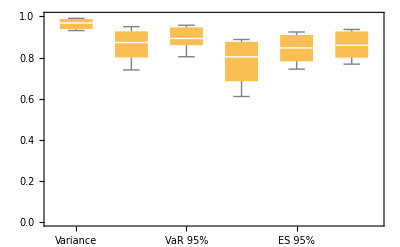

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

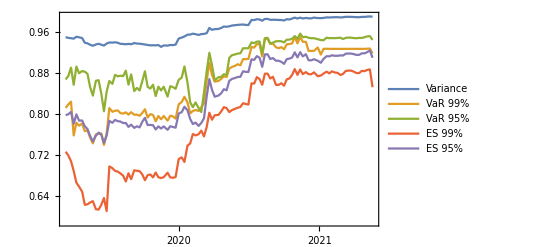

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

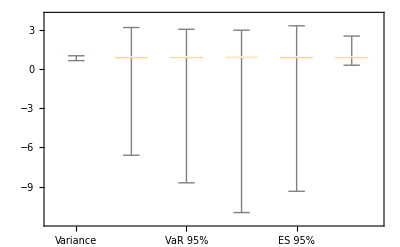

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

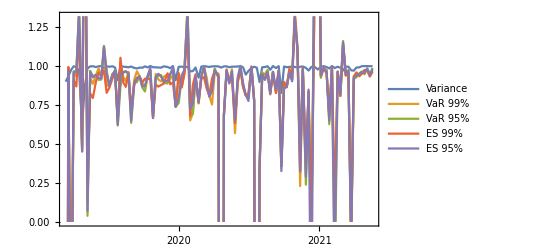

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,7]]
```

log return bitcoin

```mathematica
data[[1,6]]
```

log return future

```mathematica
data[[2,2]]
```

2019-03-11 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BTC Price | log return future | log return bitcoin
560 | 2019-03-11 20:00:00+00:00 | 3835. | BTCJ19 Curncy | 3841.83 | -0.0142397 | -0.0137756
561 | 2019-03-08 21:00:00+00:00 | 3890. | BTCJ19 Curncy | 3895.12 | 0.00644748 | 0.00617449
562 | 2019-03-07 21:00:00+00:00 | 3865. | BTCJ19 Curncy | 3871.15 | 0.00648932 | 0.00814132
563 | 2019-03-06 21:00:00+00:00 | 3840. | BTCJ19 Curncy | 3839.76 | 0.00260756 | -0.00454234
564 | 2019-03-05 21:00:00+00:00 | 3830. | BTCJ19 Curncy | 3857.24 | 0.0358842 | 0.0377644
565 | 2019-03-04 21:00:00+00:00 | 3695. | BTCJ19 Curncy | 3714.29 | -0.0332699 | -0.0304089
566 | 2019-03-01 21:00:00+00:00 | 3820. | BTCJ19 Curncy | 3828.97 | 0.0078844 | 0.00664576
567 | 2019-02-28 21:00:00+00:00 | 3790. | BTCH19 Curncy | 3803.61 | 0.0213341 | 0.0190701
568 | 2019-02-27 21:00:00+00:00 | 3710. | BTCH19 Curncy | 3731.76 | -0.0173685 | -0.0162427)

```mathematica
hvec
```

{{2019-03-11},{0.975732},{0.957384},{0.999247},{0.960651},{1.03466},{0.971906},{{0.030902988460698083, {h$798250857 -> 0.9573835789539975}},{0.011831971671533922, {h$798250857 -> 0.9992474112227664}},{0.052259505929807167, {h$798250857 -> 0.9606510147974774}},{0.024937839087606786, {h$798250857 -> 1.0346556358141232}},{0.014224930859666335, {h$798250857 -> 0.9719059650490258}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

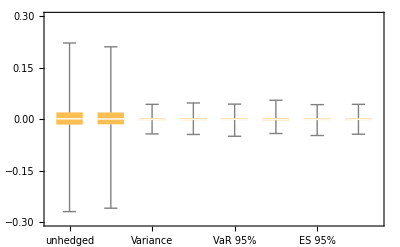

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

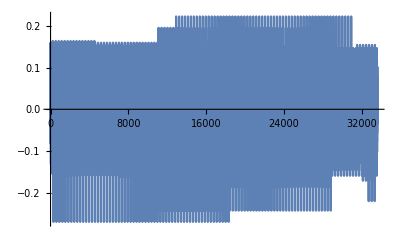

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

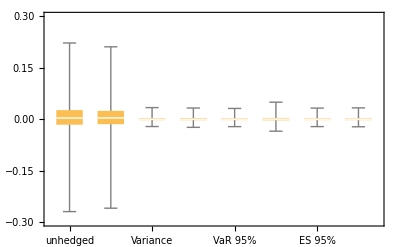

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

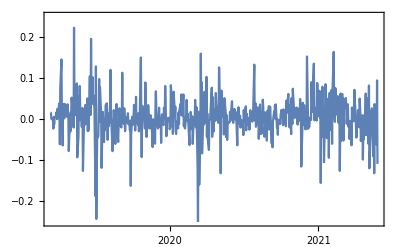
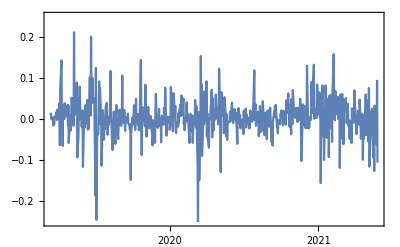

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

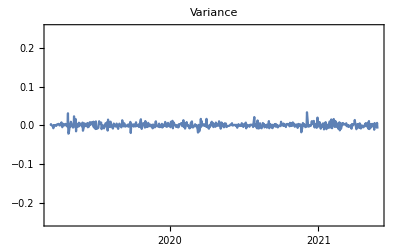
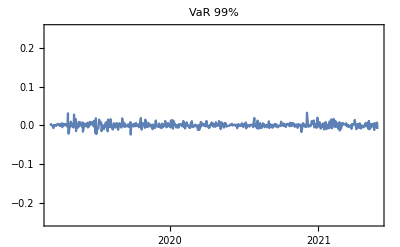
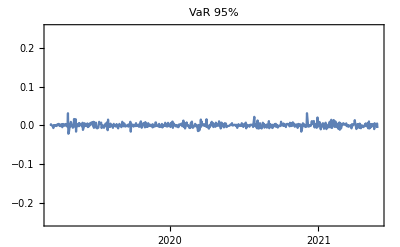
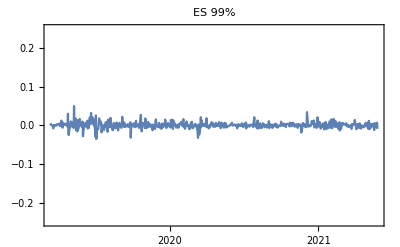
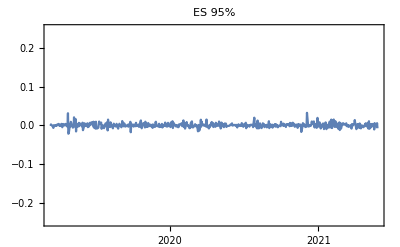
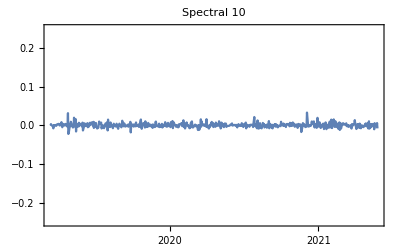

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

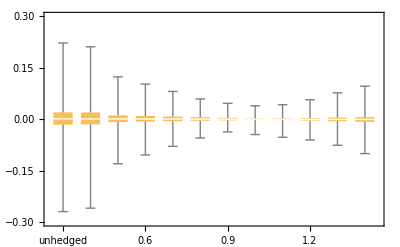

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

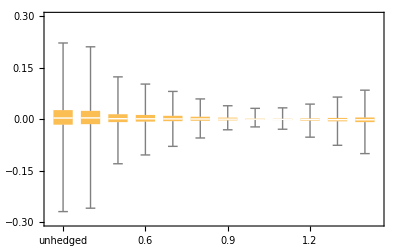

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤111, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.944958 | 0.936403 | 0.960422 | 0.939858 | 0.95253 | 0.949929
2021-05-13 | 0.944997 | 0.939292 | 0.95798 | 0.939858 | 0.950929 | 0.955053
2021-05-06 | 0.944795 | 0.939567 | 0.957988 | 0.939858 | 0.950902 | 0.955056
2021-04-29 | 0.945655 | 0.939858 | 0.957783 | 0.939858 | 0.951419 | 0.953189
2021-04-22 | 0.945022 | 0.939858 | 0.956836 | 0.939858 | 0.951895 | 0.95783
2021-04-15 | 0.943477 | 0.939858 | 0.957584 | 0.939858 | 0.950425 | 0.956884
2021-04-08 | 0.943478 | 0.939858 | 0.957346 | 0.939858 | 0.950425 | 0.957729
2021-04-01 | 0.944295 | 0.939858 | 0.957436 | 0.939858 | 0.950425 | 0.960253
2021-03-25 | 0.944517 | 0.939858 | 0.957748 | 0.939858 | 0.950425 | 0.957551
2021-03-18 | 0.944912 | 0.939858 | 0.958286 | 0.939858 | 0.950425 | 0.951931
2021-03-11 | 0.944109 | 0.939858 | 0.95762 | 0.939858 | 0.950425 | 0.949216
2021-03-04 | 0.9438 | 0.939858 | 0.957367 | 0.939858 | 0.950425 | 0.951002
2021-02-25 | 0.942553 | 0.939858 | 0.957789 | 0.939858 | 0.950686 | 0.951244
2021-02-18 | 0.943591 | 0.939858 | 0.957953 | 0.939858 | 0.950722 | 0.952645
2021-02-10 | 0.943575 | 0.939858 | 0.957789 | 0.939858 | 0.950686 | 0.951534
2021-02-03 | 0.942488 | 0.939858 | 0.957548 | 0.939858 | 0.950425 | 0.948618
2021-01-27 | 0.943994 | 0.939858 | 0.957388 | 0.939858 | 0.950425 | 0.951436
2021-01-20 | 0.943575 | 0.933217 | 0.957789 | 0.939858 | 0.950425 | 0.94659
2021-01-12 | 0.942291 | 0.939858 | 0.958821 | 0.939858 | 0.950425 | 0.951074
2021-01-05 | 0.937763 | 0.939858 | 0.926461 | 0.939858 | 0.941973 | 0.950224
2020-12-28 | 0.939688 | 0.942848 | 0.935498 | 0.931769 | 0.950043 | 0.948606
2020-12-18 | 0.938988 | 0.930508 | 0.940857 | 0.930508 | 0.948615 | 0.948099
2020-12-11 | 0.937418 | 0.930508 | 0.93659 | 0.929982 | 0.948912 | 0.948502
2020-12-04 | 0.937351 | 0.930508 | 0.937615 | 0.930508 | 0.948485 | 0.945604
2020-11-27 | 0.940641 | 0.949384 | 0.958542 | 0.937226 | 0.951376 | 0.946668
2020-11-19 | 0.941777 | 0.948722 | 0.958542 | 0.935753 | 0.951305 | 0.948856
2020-11-12 | 0.942044 | 0.96104 | 0.940723 | 0.953136 | 0.953458 | 0.943633
2020-11-05 | 0.940802 | 0.942962 | 0.934453 | 0.927417 | 0.950425 | 0.939673
2020-10-29 | 0.94099 | 0.96104 | 0.937759 | 0.952019 | 0.951658 | 0.943262
2020-10-22 | 0.940562 | 0.939867 | 0.93415 | 0.926782 | 0.950425 | 0.940401
2020-10-15 | 0.938923 | 0.938557 | 0.93375 | 0.926837 | 0.950425 | 0.940648
2020-10-08 | 0.939694 | 0.942708 | 0.933299 | 0.928603 | 0.950344 | 0.941757
2020-10-01 | 0.937485 | 0.924236 | 0.929361 | 0.922275 | 0.949601 | 0.939241
2020-09-24 | 0.937893 | 0.926261 | 0.924532 | 0.923896 | 0.950097 | 0.942868
2020-09-17 | 0.938604 | 0.943226 | 0.929538 | 0.923896 | 0.949641 | 0.944185
2020-09-10 | 0.938103 | 0.928079 | 0.929361 | 0.924417 | 0.949641 | 0.939386
2020-09-02 | 0.946997 | 0.96261 | 0.952165 | 0.959915 | 0.969274 | 0.938439
2020-08-26 | 0.951508 | 0.974346 | 0.95186 | 0.957458 | 0.968364 | 0.948049
2020-08-19 | 0.952679 | 0.968305 | 0.934266 | 0.966517 | 0.969688 | 0.948099
2020-08-12 | 0.952895 | 0.967749 | 0.934488 | 0.966633 | 0.969688 | 0.948492
2020-08-05 | 0.95096 | 0.941415 | 0.946592 | 0.95572 | 0.961297 | 0.945351
2020-07-29 | 0.952553 | 0.973319 | 0.952524 | 0.957899 | 0.968558 | 0.950066
2020-07-22 | 0.955108 | 0.973169 | 0.950411 | 0.958416 | 0.968558 | 0.954573
2020-07-15 | 0.953608 | 0.958604 | 0.956209 | 0.952615 | 0.967411 | 0.962158
2020-07-08 | 0.954 | 0.960096 | 0.957235 | 0.953315 | 0.967629 | 0.952328
2020-06-30 | 0.948643 | 0.938719 | 0.948944 | 0.935451 | 0.964035 | 0.946958
2020-06-23 | 0.948852 | 0.937191 | 0.948944 | 0.935109 | 0.964034 | 0.947431
2020-06-16 | 0.949394 | 0.93732 | 0.948944 | 0.935916 | 0.964202 | 0.947068
2020-06-09 | 0.950762 | 0.928101 | 0.944033 | 0.926849 | 0.963285 | 0.965948
2020-06-02 | 0.950521 | 0.931507 | 0.943374 | 0.927556 | 0.96335 | 0.965397
2020-05-26 | 0.950143 | 0.985633 | 0.946615 | 0.924463 | 0.961017 | 0.964796
2020-05-18 | 0.949726 | 0.973912 | 0.946639 | 0.923013 | 0.961372 | 0.964141
2020-05-11 | 0.949043 | 0.924443 | 0.942083 | 0.922073 | 0.961265 | 0.962554
2020-05-04 | 0.948231 | 0.939595 | 0.952671 | 0.957876 | 0.952671 | 0.953638
2020-04-27 | 0.948305 | 0.943333 | 0.948617 | 0.965464 | 0.953125 | 0.94799
2020-04-20 | 0.947418 | 0.932229 | 0.951637 | 0.967081 | 0.956018 | 0.948411
2020-04-13 | 0.946247 | 0.974895 | 0.94906 | 0.963845 | 0.950352 | 0.948831
2020-04-03 | 0.946647 | 0.972179 | 0.948412 | 0.962009 | 0.956572 | 0.953347
2020-03-27 | 0.946869 | 1.00313 | 0.957267 | 0.931201 | 0.965361 | 0.955997
2020-03-20 | 0.948047 | 0.932019 | 0.945609 | 0.927565 | 0.961887 | 0.954419
2020-03-13 | 0.940912 | 0.990325 | 0.951484 | 0.915055 | 0.954039 | 0.948019
2020-03-06 | 0.952808 | 0.981084 | 0.969034 | 0.894546 | 0.966617 | 0.981311
2020-02-28 | 0.951281 | 0.974535 | 0.928525 | 0.92524 | 0.949669 | 0.972828
2020-02-21 | 0.945766 | 0.96834 | 0.929343 | 0.912902 | 0.947423 | 0.944412
2020-02-13 | 0.947609 | 0.972418 | 0.96335 | 0.907758 | 0.954059 | 0.954091
2020-02-06 | 0.949967 | 0.968464 | 0.969217 | 0.910579 | 0.947851 | 0.970498
2020-01-30 | 0.945028 | 0.987854 | 0.964551 | 0.894115 | 0.956116 | 0.950736
2020-01-23 | 0.945315 | 0.991206 | 0.973714 | 0.889839 | 0.962378 | 0.951877
2020-01-15 | 0.943978 | 0.895572 | 0.975917 | 0.890487 | 0.97419 | 0.956251
2020-01-08 | 0.942792 | 0.888685 | 0.981181 | 0.884826 | 0.965118 | 0.936911
2019-12-31 | 0.942787 | 0.903469 | 0.979171 | 0.883563 | 0.964381 | 0.954428
2019-12-23 | 0.937528 | 0.905962 | 0.962848 | 0.858632 | 0.958957 | 0.942796
2019-12-16 | 0.940426 | 0.906818 | 0.965785 | 0.862065 | 0.960032 | 0.948748
2019-12-09 | 0.940839 | 0.896899 | 0.965173 | 0.862906 | 0.960506 | 0.947723
2019-12-02 | 0.940577 | 0.928648 | 0.964508 | 0.859172 | 0.955141 | 0.94551
2019-11-22 | 0.941498 | 0.908013 | 0.984811 | 0.862425 | 0.960168 | 0.95208
2019-11-15 | 0.939936 | 0.90337 | 0.978352 | 0.85984 | 0.958581 | 0.95817
2019-11-08 | 0.941661 | 0.907919 | 0.985419 | 0.86262 | 0.960159 | 0.952459
2019-11-01 | 0.941527 | 0.929728 | 0.967677 | 0.859583 | 0.955072 | 0.948766
2019-10-25 | 0.942203 | 0.900304 | 0.973538 | 0.865457 | 0.961747 | 0.950274
2019-10-18 | 0.942618 | 0.921892 | 0.977259 | 0.867404 | 0.962414 | 0.946753
2019-10-11 | 0.943893 | 0.922422 | 0.966945 | 0.863127 | 0.960883 | 0.952272
2019-10-04 | 0.944615 | 0.976721 | 0.989154 | 0.87093 | 0.971163 | 0.954409
2019-09-27 | 0.945315 | 0.907969 | 0.978127 | 0.867928 | 0.964172 | 0.954875
2019-09-20 | 0.94772 | 0.918224 | 0.971904 | 0.862493 | 0.961773 | 0.958886
2019-09-13 | 0.94814 | 0.91219 | 0.976634 | 0.867404 | 0.962962 | 0.955369
2019-09-06 | 0.949256 | 0.900032 | 0.966959 | 0.86491 | 0.961401 | 0.963012
2019-08-29 | 0.948447 | 0.905568 | 0.983225 | 0.86835 | 0.967502 | 0.960036
2019-08-22 | 0.949349 | 0.897549 | 0.9765 | 0.866493 | 0.962111 | 0.953764
2019-08-15 | 0.949441 | 0.902986 | 0.982439 | 0.867701 | 0.967015 | 0.959643
2019-08-08 | 0.950159 | 0.897288 | 0.988252 | 0.865484 | 0.963519 | 0.969646
2019-08-01 | 0.950575 | 0.898312 | 0.990852 | 0.869066 | 0.963959 | 0.967383
2019-07-25 | 0.952708 | 0.904081 | 0.977705 | 0.873133 | 0.963862 | 0.962677
2019-07-18 | 0.954122 | 0.912066 | 0.986841 | 0.872194 | 0.964292 | 0.963211
2019-07-11 | 0.954632 | 0.904948 | 0.981671 | 0.877109 | 0.962495 | 0.970682
2019-07-03 | 0.955577 | 0.909995 | 0.971198 | 0.877107 | 0.963871 | 0.963649
2019-06-26 | 0.952699 | 0.890509 | 0.977367 | 0.83414 | 0.959233 | 0.983879
2019-06-19 | 0.948754 | 0.94835 | 0.955752 | 0.823502 | 0.950703 | 0.959149
2019-06-12 | 0.949835 | 0.940703 | 0.976824 | 0.831524 | 0.963893 | 0.963056
2019-06-05 | 0.952382 | 0.936468 | 0.973488 | 0.829031 | 0.967053 | 0.959272
2019-05-29 | 0.953816 | 0.9319 | 0.973078 | 0.828212 | 0.966652 | 0.960235
2019-05-21 | 0.952927 | 0.910769 | 0.960888 | 0.817208 | 0.952976 | 0.961782
2019-05-14 | 0.954353 | 0.925084 | 0.97557 | 0.824959 | 0.960902 | 0.957063
2019-05-07 | 0.958395 | 0.938385 | 0.988898 | 0.842331 | 0.969916 | 0.974121
2019-04-30 | 0.959189 | 0.931491 | 0.989477 | 0.853378 | 0.973908 | 0.958102
2019-04-23 | 0.968071 | 0.960433 | 0.976322 | 0.889152 | 0.973911 | 0.987324
2019-04-15 | 0.968985 | 0.966333 | 0.990623 | 0.899854 | 0.973283 | 0.97487
2019-04-08 | 0.968988 | 0.953813 | 0.982515 | 0.885351 | 0.982884 | 0.978232
2019-04-01 | 0.967466 | 0.983798 | 0.997575 | 0.937425 | 0.992702 | 0.963878
2019-03-25 | 0.975057 | 0.964903 | 1.06264 | 0.954191 | 1.02416 | 0.971195
2019-03-18 | 0.974561 | 0.996531 | 0.998379 | 0.952044 | 1.0254 | 0.95721
2019-03-11 | 0.975732 | 0.957384 | 0.999247 | 0.960651 | 1.03466 | 0.971906)

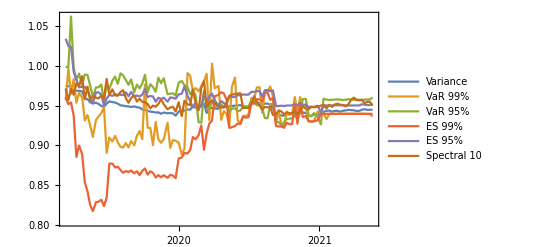

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```